# BCS theory – numerical solution of self-consistency equation

### For the analytical part, we need:

For T_c we need:

```mathematica
Integrate[Log[x]/(Cosh[x])^2,{x,0,∞}]
```

-EulerGamma+Log[π/4]

### Let’s solve the self-consistency equations numerically:

Now, let’s solve the self-consistency equations numerically: 
Here both T and Δ are in units of the Debye energy; gρsh is a list of values of ρ_F g/2 plotted.
The gray dots are the corresponding analytic results for T_c and Δ(T=0). Clearly, we obtain very good agreement.

```mathematica
KeyInteg[Δ_,T_]:=NIntegrate[Tanh[(√(x^2+Δ^2))/(2 T)]/(√(x^2+Δ^2)),{x,0,1}]
```

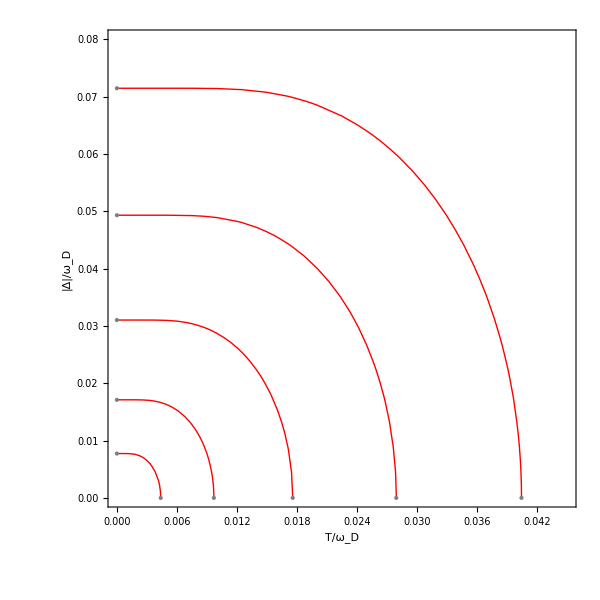

```mathematica
gρsh={0.3,0.27,0.24,0.21,0.18};

Δs=Table[{0,1/Sinh[1/gρ]},{gρ,gρsh}];
Tcs=Table[{(2Exp[EulerGamma])/π Exp[-1/gρ],0},{gρ,gρsh}];
Show[ContourPlot[1/KeyInteg[Δ,T],{T,0.00001,0.045},{Δ,0.00001,0.08},PlotPoints->10,Contours->gρsh,ContourShading->None,ContourLabels->None,ContourLabels->Function[{x,y,z},Text[Framed[z],{x,y},Background->White]],LabelStyle->Large,ImageSize->600,ContourStyle->Directive[Thick,Red],FrameStyle->Thick,PlotLegends->Automatic,FrameLabel->{"T/ω_D","|Δ|/ω_D"}],Graphics[{PointSize[Large],Gray,Point[Δs],Point[Tcs]}]]
```

Let’s take a more systematic look at the deviations:

a) Low temperature behavior is exponential:

```mathematica
gρshV=0.3;
ΔT0=1/Sinh[1/gρshV];
DeltaN[T_]:=FindRoot[KeyInteg[Δ,T]-1/gρshV,{Δ,ΔT0}]//Quiet
```

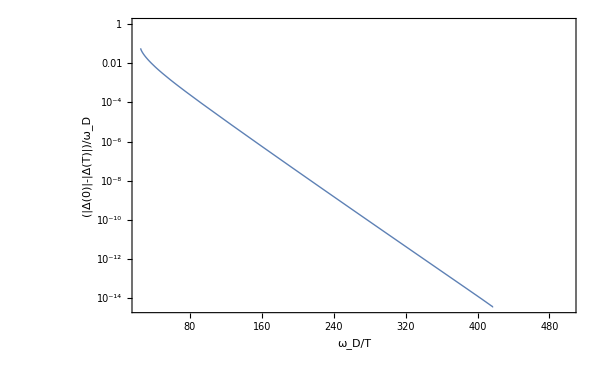

```mathematica
LogPlot[ΔT0-Δ/.DeltaN[1/InvT],{InvT,25,500},PlotPoints->15,Frame->True,FrameLabel->{"ω_D/T","(|Δ(0)|-|Δ(T)|)/ω_D"},FrameStyle->Thick,LabelStyle->Large,ImageSize->600,PlotStyle->Thick]
```

b) The onset behavior is square-root-like:

```mathematica
gρshV=0.3;
DeltaN[T_]:=FindRoot[KeyInteg[Δ,T]-1/gρshV,{Δ,ΔT0}]//Quiet
```

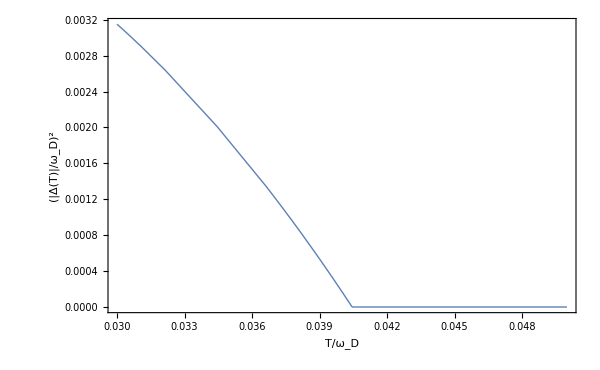

```mathematica
Plot[Δ^2/.DeltaN[T],{T,0.03,0.05},PlotPoints->10,Frame->True,FrameLabel->{"T/ω_D","(|Δ(T)|/ω_D)^2"},FrameStyle->Thick,LabelStyle->Large,ImageSize->600,PlotStyle->Thick]
```